Μετατοπίσεις κόμβων στο καθολικό σύστημα.
{{0.,0.},{0.000847779,0.00837168}}

Αντιδράσεις στηρίξεων σε κόμβους (οι ελαστικές στηρίξεις επιστρέφουν αντίδραση μηδέν).
 {{250.795,-125.397},{-250.795,25.3974}}

Επιμηκύνσεις των ράβδων:
{-0.00298565}

Αξονικές δυνάμεις των ράβδων (επιμηκύνσεις+προεντάσεις):
{-280.397}

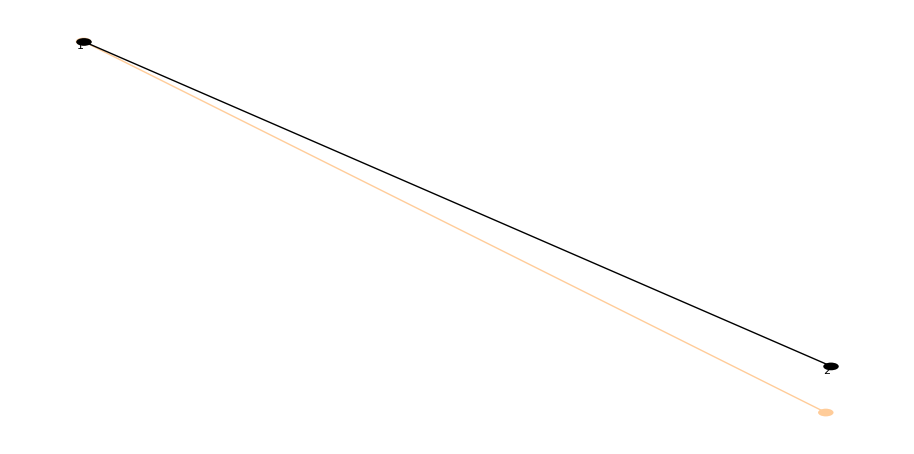

```mathematica
(* ΕΠΙΛΥΣΗ ΓΕΝΙΚΕΥΜΕΝΟΥ ΔΙΚΤΥΩΜΑΤΟΣ 2D,
ΠΡΟΓΡΑΜΜΑΤΙΣΜΟΣ: ΠΑΥΛΟΣ ΓΚΕΣΟΣ (ΣΣΕ 2002),
ΕΤΟΣ: 2011,
ΑΔΕΙΑ ΧΡΗΣΗΣ: BSD,
ΣΧΟΛΗ: ΣΤΕΑΜΧ,
Είναι σπάνιο σε ένα πρόγραμμα όσο απλό κι αν είναι να μην βρεθούν bugs. Αν βρείτε κάτι επικοινωνήστε μαζί μου gessos.paul@gmail.com *)

(* -=-=-=-=-=-=-=- ΟΡΙΣΜΟΣ ΔΕΔΟΜΕΝΩΝ (ορισμένα δεδομένα ορίζονται πιο κάτω) -=-=-=-=-=-=-=- *)
Clear[i,j,k,P,K,EA];
P=100;K=5000;
EA=2.1 10^8 10 10^-4; (* Ε×Α *)
(* Πόσες φορές θα μεγεθυνθεί η παραμόρφωση προκειμένου να είναι ορατή από το ανθρώπινο μάτι στο σχέδιο *)
displacementZoom=15;
(* Κόμβοι: X, Y *)
joints={{0,0},{2,-1}};
(* Κόμβοι: [Βαθμός ελευθερίας στον Χ, Βαθμός ελευθερίας στον Y [, Γωνία Χ-Υ [0°,90°) σε σχέση με το καθολικό Χ-Υ ] ]
Ο βαθμός ελευθερίας είναι 0 αν κινείται ελεύθερα, +∞ αν δεν κινείται, μια σταθερά ελατηρίου σε άλλη περίπτωση
Αν η γωνία είναι 0 να παραλείπεται. Αν οι βαθμοί ελευθερίας είναι 0 να παραλείπονται και να μπαίνει Null *)
jointsx={{+∞,+∞},{0,+∞,14.03624346792647858289232016}};
(* Ράβδοι: Κόμβος1, Κόμβος2, Ε×Α *)
bars={{1,2, EA}};
(* Εξωτερικές δυνάμεις στους κόμβους, στο καθολικό σύστημα αναφοράς: Χ, Υ *)
forces={{0,0},{0,P}};
(* Υποχωρήσεις στηρίξεων, στο καθολικό σύστημα αναφοράς: Κόμβος, Χ, Υ *)
displacements={(*{2,-.01,0}*)};
(* -=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=- *)

(* Υπολογισμός μηκών ράβδων από κόμβο σε κόμβο *)
lengths=Simplify[Table[Norm[joints⟦bars⟦ii,2⟧⟧-joints⟦bars⟦ii,1⟧⟧],{ii,Length[bars]}]];

(* -=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=- ΟΡΙΣΜΟΣ ΔΕΔΟΜΕΝΩΝ -=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=- *)
(* Προεντάσεις (σε ανυγμένη παραμόρφωση) από θερμοκρασιακές μεταβολές, ελλατωματικά μέλη ή προένταση μέλους *)
strains={0};
(* -=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=-=- *)
reinforcement=Table[{-strains⟦ii⟧bars⟦ii,3⟧,0},{ii,Length[bars]}];

(* ==== Πίνακες στροφής 2x2 από το τοπικό σύστημα της ράβδου στο καθολικό του φορέα ==== *)
(*Print["Rotation Matrices from Global to Local:"];*)
rot2=Simplify[Table[({{tmp1=(joints⟦bars⟦ii,2⟧,1⟧-joints⟦bars⟦ii,1⟧,1⟧)/lengths⟦ii⟧, tmp2=(joints⟦bars⟦ii,2⟧,2⟧-joints⟦bars⟦ii,1⟧,2⟧)/lengths⟦ii⟧}, {-tmp2, tmp1}}),{ii,Length[bars]}]];
(*Do[Print[MatrixForm[rot2⟦ii⟧]],{ii,Length[rot2]}]*)

(* ==== Τοπικό μητρώο 4x4 δυσκαμψίας της ράβδου ==== *)
(*Print["Local Stiffness Matrices:"];*)
stiffnessL=Simplify[Table[({{tmp1=bars⟦ii,3⟧/lengths⟦ii⟧, 0, -tmp1, 0}, {0, 0, 0, 0}, {-tmp1, 0, tmp1, 0}, {0, 0, 0, 0}}),{ii,Length[bars]}]];
(*Do[Print[MatrixForm[stiffnessL⟦ii⟧]],{ii,Length[stiffnessL]}]*)

(* ==== Ελατηριωτές στηρίξεις ==== *)
bars2=bars; (* backup! *)
rotBsupport=IdentityMatrix[2Length[joints]];
Do[
(* Ούτε ελατήριο - ούτε πλάγια κύλιση: δεν κάνουμε τίποτα *)
If[jointsx⟦ii⟧===Null||jointsx⟦ii,1⟧==jointsx⟦ii,2⟧==0||jointsx⟦ii,1⟧==jointsx⟦ii,2⟧==+∞||
(Length[jointsx⟦ii⟧]==2||jointsx⟦ii,3⟧==0)&&(jointsx⟦ii,1⟧==0&&jointsx⟦ii,2⟧==+∞||jointsx⟦ii,1⟧==+∞&&jointsx⟦ii,2⟧==0),(* do nothing *),
(* Πίνακας στροφής *)
If[Length[jointsx⟦ii⟧]==3,tmp1=Cos[jointsx⟦ii,3⟧];tmp2=Sin[jointsx⟦ii,3⟧],tmp1=1;tmp2=0];
rotSup=({{tmp1, tmp2}, {-tmp2, tmp1}});
(* Αν έχουμε δέσμευση μετακίνησης σε πλάγιο άξονα κρατάμε τον πίνακα στροφής για να ξέρουμε πως γίνεται η μετατόπιση *)
If[Length[jointsx⟦ii⟧]==3&&jointsx⟦ii,3⟧≠0&&(jointsx⟦ii,1⟧==+∞||jointsx⟦ii,2⟧==+∞),rotBsupport⟦2ii-1;;2ii,2ii-1;;2ii⟧=rotSup];
(* Extra δοκός *)
If[jointsx⟦ii,1⟧==0&&jointsx⟦ii,2⟧==+∞||jointsx⟦ii,1⟧==+∞&&jointsx⟦ii,2⟧==0,(* do nothing *),
rot2=Append[rot2,rotSup];bars=Append[bars,{ii,ii}];reinforcement=Append[reinforcement,{0,0}];
(* Σκληρότητα ελατηρίου(ων) στο τοπικό σύστημα *)
stiffnessL=Append[stiffnessL,({{If[jointsx⟦ii,1⟧≠+∞,jointsx⟦ii,1⟧,0], 0, 0, 0}, {0, If[jointsx⟦ii,2⟧≠+∞,jointsx⟦ii,2⟧,0], 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})];
]
],{ii,Length[joints]}];
MatrixForm[rotBsupport];

(* ==== Πίνακες στροφής 4x4 από το τοπικό σύστημα της ράβδου στο καθολικό του φορέα ==== *)
(*Print["Rotation Matrices 4x4 from Global to Local:"];*)
rot4=Table[({{rot2⟦ii,1,1⟧, rot2⟦ii,1,2⟧, 0, 0}, {rot2⟦ii,2,1⟧, rot2⟦ii,2,2⟧, 0, 0}, {0, 0, rot2⟦ii,1,1⟧, rot2⟦ii,1,2⟧}, {0, 0, rot2⟦ii,2,1⟧, rot2⟦ii,2,2⟧}}),{ii,Length[bars]}];
(*Do[Print[MatrixForm[rot4⟦ii⟧]],{ii,Length[rot4]}]*)

(* ==== Μητρώο 4x4 δυσκαμψίας της ράβδου στο καθολικό σύστημα ==== *)
(*Print["Global Stiffness Matrices:"];*)
stiffnessG=Simplify[Table[Transpose[rot4⟦ii⟧].stiffnessL⟦ii⟧.rot4⟦ii⟧,{ii,Length[bars]}]];
(*Do[Print[MatrixForm[stiffnessG⟦ii⟧]],{ii,Length[stiffnessG]}]*)

(* ==== Ολικό μητρώο δυσκαμψίας του φορέα στο καθολικό σύστημα ==== *)
(*Print["Body Stiffness Matrix:"];*)
stiffnessB=Table[Table[0,{2 Length[joints]}],{2 Length[joints]}];
Do[Do[Do[stiffnessB⟦2 bars⟦ii,Floor[(jj-1)/2+1]⟧-1+Floor[Mod[jj-1,2]],2 bars⟦ii,Floor[(kk-1)/2+1]⟧-1+Floor[Mod[kk-1,2]]⟧+=stiffnessG⟦ii,jj,kk⟧
,{kk,4}],{jj,4}],{ii,Length[bars]}];
MatrixForm[stiffnessB];
(* Περιστροφή στο ολικό μητρώο δυσκαμψίας του φορέα, των δυσκαμψιών των πλάγιων στηρίξεων *)
stiffnessB=rotBsupport.stiffnessB.Transpose[rotBsupport];
MatrixForm[stiffnessB];

(* ==== Πίνακας δυνάμεων κόμβων ==== *)
forces2=forces;
(* Στροφή των προεντάσεων στο καθολικό σύστημα αναφοράς *)
reinforcements2=Table[Transpose[rot2⟦ii⟧].reinforcement⟦ii⟧,{ii,Length[bars]}];
(* Αφαίρεση των προεντάσεων των ράβδων από τον κόμβο *)
Do[forces2⟦bars⟦ii,1⟧⟧+=reinforcements2⟦ii⟧,{ii,Length[bars]}];
Do[forces2⟦bars⟦ii,2⟧⟧-=reinforcements2⟦ii⟧,{ii,Length[bars]}];
(* Στροφή των επικόμβιων δυνάμεων των κόμβων πλαγίων στηρίξεων, στο τοπικό σύστημα της στήριξης *)
forces2=Flatten[forces2];
forces2=rotBsupport.forces2;

(* ==== Πίνακας μετατοπίσεων κόμβων ==== *)
displacements2=Table[{0,0},{Length[joints]}];
Do[Do[displacements2⟦displacements⟦ii,1⟧,jj⟧=displacements⟦ii,jj+1⟧,{jj,2}],{ii,Length[displacements]}];
(* Στροφή των μετατοπίσεων των κόμβων πλαγίων στηρίξεων, στο τοπικό σύστημα της στήριξης *)
displacements2=Flatten[displacements2];
displacements2=rotBsupport.displacements2;

(* ==== Πίνακας-στήλη αναδιάταξης ==== *)
rearrangement={{},{}};
Do[If[jointsx⟦ii⟧===Null,rearrangement⟦1⟧=Join[rearrangement⟦1⟧,{2ii-1,2ii}],
Do[If[jointsx⟦ii,jj⟧≠+∞,rearrangement⟦1⟧=Append[rearrangement⟦1⟧,2ii-2+jj],rearrangement⟦2⟧=Append[rearrangement⟦2⟧,2ii-2+jj]],{jj,2}]
],{ii,Length[joints]}];
(*Print["Rearrangement Column-Matrix: ",rearrangement];*)

(* ==== Εύρεση των τμημάτων των πινάκων F, K και Δ ==== *)
(* Η πρώτη λίστα είναι οι γνωστές κομβικές δυνάμεις. Η δεύτερη είναι οι προεντάσεις και εξωτερικά φορτία πάνω σε κόμβους δίχως τις άγνωστες αντιδράσεις. *)
forcesM=Table[Table[forces2⟦rearrangement⟦jj,ii⟧⟧,{ii,Length[rearrangement⟦jj⟧]}],{jj,2}];
(* Η πρώτη λίστα είναι οι άγνωστες κομβικές μετατοπίσεις. Η δεύτερη είναι οι γνωστές. *)
displacementsΜ={Null,Table[displacements2⟦rearrangement⟦2,ii⟧⟧,{ii,Length[rearrangement⟦2⟧]}]};
(* Οι 4 πίνακες FF, FS, SF, SS. *)
stiffnessBΜ=Table[Table[Table[Table[stiffnessB⟦rearrangement⟦ll,ii⟧,rearrangement⟦kk,jj⟧⟧,{jj,Length[rearrangement⟦kk⟧]}],{ii,Length[rearrangement⟦ll⟧]}],{kk,2}],{ll,2}];
(* ==== Επίλυση για τις μετατοπίσεις ==== *)
displacementsΜ⟦1⟧=FullSimplify[Inverse[stiffnessBΜ⟦1,1⟧].(forcesM⟦1⟧-stiffnessBΜ⟦1,2⟧.displacementsΜ⟦2⟧)];
(* Επίλυση για τις αντιδράσεις: Αφαιρούνται από την επίδραση στον κόμβο εξωτερικές δυνάμεις και προεντάσεις *)
forcesM⟦2⟧=FullSimplify[stiffnessBΜ⟦2,1⟧.displacementsΜ⟦1⟧+stiffnessBΜ⟦2,2⟧.displacementsΜ⟦2⟧-forcesM⟦2⟧];
forcesM⟦1⟧*=0;

(* ==== Επαναδιάταξη ως αρχικά των μετατοπίσεων κόμβων ==== *)
displacements=Table[0,{ii,2Length[joints]}];
Do[Do[displacements⟦rearrangement⟦jj,ii⟧⟧=displacementsΜ⟦jj,ii⟧,{ii,Length[rearrangement⟦jj⟧]}],{jj,2}];
(* Στροφή των μετατοπίσεων των κόμβων πλαγίων στηρίξεων, από το τοπικό σύστημα της στήριξης στο καθολικό *)
displacements=Transpose[rotBsupport].displacements;
displacements=Partition[displacements,2];

(* ==== Επαναδιάταξη ως αρχικά των επικόμβιων δυνάμεων. Οι αντιδράσεις ελαστικών στηρίξεων εμφανίζονται ως μηδέν επειδή εκφράζονται σε μετατοπίσεις ==== *)
forces2=Table[0,{ii,2Length[joints]}];
Do[Do[forces2⟦rearrangement⟦jj,ii⟧⟧=forcesM⟦jj,ii⟧,{ii,Length[rearrangement⟦jj⟧]}],{jj,2}];
(* ################################################################################### ΠΡΕΠΕΙ ΝΑ ΤΟΠΟΘΕΤΗΣΩ ΕΔΩ ΤΙΣ ΑΝΤΙΔΡΑΣΕΙΣ ΕΛΑΣΤΙΚΩΝ ΣΤΗΡΙΞΕΩΝ ΜΕ ΒΑΣΗ ΤΙΣ ΜΕΤΑΤΟΠΙΣΕΙΣ #### *)
(* Στροφή των μετατοπίσεων των κόμβων πλαγίων στηρίξεων, από το τοπικό σύστημα της στήριξης στο καθολικό *)
forces2=Transpose[rotBsupport].forces2;
forces2=Partition[forces2,2];

(* Υπολογισμός αξονικών επιμηκύνσεων στο τοπικό σύστημα *)
displacementsL=Table[(rot2⟦ii⟧.(displacements⟦bars⟦ii,2⟧⟧-displacements⟦bars⟦ii,1⟧⟧))⟦1⟧,{ii,Length[bars2]}];
(* Υπολογισμός αξονικών δυνάμεων στο τοπικό σύστημα *)
axialforcesL=Table[(displacementsL⟦ii⟧/lengths⟦ii⟧-strains⟦ii⟧)bars⟦ii,3⟧,{ii,Length[bars2]}];


(* ΕΞΟΔΟΙ ΔΕΔΟΜΕΝΩΝ!!! *)
Print["\nΜετατοπίσεις κόμβων στο καθολικό σύστημα.\n",FullSimplify[displacements]];
Print["\nΑντιδράσεις στηρίξεων σε κόμβους (οι ελαστικές στηρίξεις επιστρέφουν αντίδραση μηδέν).\n ",FullSimplify[forces2]];
Print["\nΕπιμηκύνσεις των ράβδων:\n",FullSimplify[displacementsL]];
Print["\nΑξονικές δυνάμεις των ράβδων (επιμηκύνσεις+προεντάσεις):\n",FullSimplify[axialforcesL]];

(* ==== ΖΩΓΡΑΦΙΕΣ!!! ==== *)
bodyStart=Table[Line[{joints⟦bars⟦ii,1⟧⟧,joints⟦bars⟦ii,2⟧⟧}],{ii,Length[bars]}];
bodyStart=Append[bodyStart,Table[Disk[joints⟦ii⟧,Scaled[0.01]],{ii,Length[joints]}]];
jointsEnd=joints+displacementZoom displacements;
bodyEnd=Table[Line[{jointsEnd⟦bars⟦ii,1⟧⟧,jointsEnd⟦bars⟦ii,2⟧⟧}],{ii,Length[bars]}];
bodyEnd=Append[bodyEnd,Table[Disk[jointsEnd⟦ii⟧,Scaled[0.01]],{ii,Length[joints]}]];
jointNums=Table[Text[Style[ii,FontSize->Scaled[0.02]],jointsEnd⟦ii⟧,{2,2}],{ii,Length[joints]}];
Graphics[{RGBColor[1,0.8,0.6],bodyStart,Black,bodyEnd, jointNums}]
```